# Homework 1

## Problem 2.3

### Graph

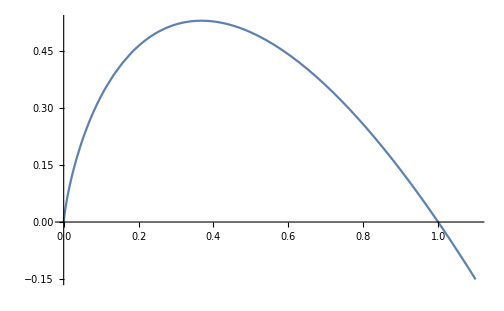

```mathematica
Plot[{-x Log[2,x]},{x,0,1.1}]
```

## Problem 2.24 (b)

### Definitions

Define a simplification function based on 0≤p≤1

```mathematica
FS24b[aa_]:=FullSimplify[aa,Assumptions->{p∈Reals,0≤p≤1}]
```

Define the binary entropy function in terms of base 2 logarithms

```mathematica
H[pp_]:=-pp Log[2,pp]-(1-pp)Log[2,(1-pp)]
H[p]//FS24b
```

((-1+p) Log[1-p]-p Log[p])/Log[2]

Define the binary entropy function in terms of natural logarithms

```mathematica
He[pp_]:=-pp Log[pp]-(1-pp)Log[1-pp]
He[p]//FS24b
```

(-1+p) Log[1-p]-p Log[p]

### Integrate

Using base 2 logarithms

```mathematica
Integrate[H[p],{p,0,1}]//FS24b
Integrate[H[p],{p,0,1}]//FS24b//N
```

1/Log[4]

0.721348

Using natural logarithms

```mathematica
Integrate[He[p],{p,0,1}]//FS24b
Integrate[He[p],{p,0,1}]//FS24b//N
```

1/2

0.5

Checking that changing from nats to bit yields the same result.

```mathematica
(1/2)Log[2,ⅇ]//N
```

0.721348